# Projected trap analysis

## image processing

```mathematica
imagedir="trapped_atoms";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

## projected trap, 808 laser + Hamamatsu

```mathematica
imagedir="trapped_atoms\\20211121\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],imagedir}]];
```

```mathematica
fnames = {"img1.csv", "img2.csv", "bg1.csv", "bg2.csv"};
```

```mathematica
img1 = Import[fnames[[1]]];
bg1   =Import[fnames[[3]]];
img1=Image[Rescale[Most/@(img1-bg1)]]
```

-Graphics-

```mathematica
img2 = Import[fnames[[2]]];
bg2  =Import[fnames[[4]]];
img2=Image[Rescale[Most/@(img2-bg2)]]
```

-Graphics-

```mathematica
Length[img1[[1]]]
```

Part::partd: Part specification … is longer than depth of object.

2

```mathematica
Show[Image[ImageData[img1][[1;;500,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,235},{512,244}]}]]
```

-Graphics-

```mathematica
Show[Image[ImageData[img2][[1;;500,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,235},{512,244}]}]]
```

-Graphics-

```mathematica
Show[Image[ImageData[img1][[255;;265,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
Show[Image[ImageData[img2][[255;;265,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
```

-Graphics-

-Graphics-

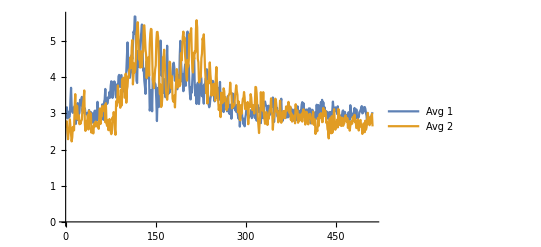

```mathematica
roi1 =ImageData[img1][[255;;265,1;;-1]];
roi2 =ImageData[img2][[255;;265,1;;-1]];
ListPlot[Total/@{roi1,roi2},PlotLegends->{"Avg 1","Avg 2"},Joined->True]
```

-Graphics-

-Graphics-

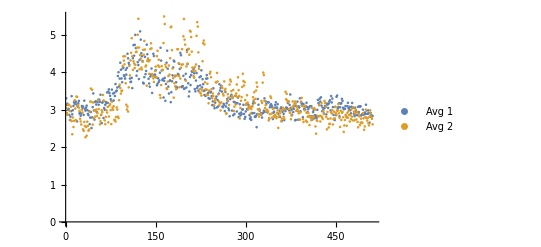

```mathematica
x1 = 265;
x2 =275;
Show[Image[ImageData[img1][[x1;;x2,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
Show[Image[ImageData[img2][[x1;;x2,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
roi1 =ImageData[img1][[x1;;x2,1;;-1]];
roi2 =ImageData[img2][[x1;;x2,1;;-1]];
ListPlot[Total/@{roi1,roi2},PlotLegends->{"Avg 1","Avg 2"},Joined->False]
```

-Graphics-

-Graphics-

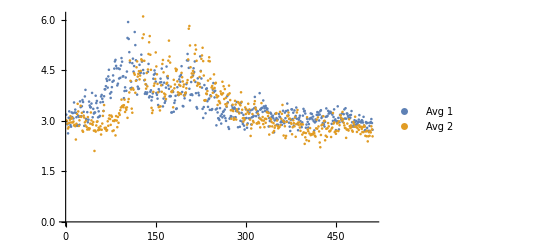

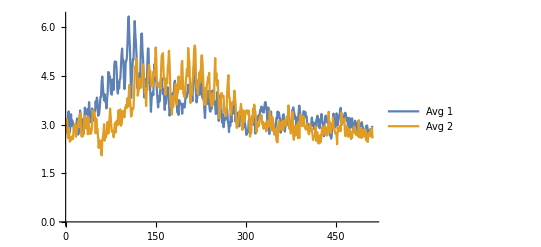

```mathematica
x1 = 235;
x2 =245;
Show[Image[ImageData[img1][[x1;;x2,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
Show[Image[ImageData[img2][[x1;;x2,1;;-1]]],Graphics[{EdgeForm[Directive[Thin,Red]], Opacity[0],Rectangle[{1,258},{512,264}]}]]
roi1 =ImageData[img1][[x1;;x2,1;;-1]];
roi2 =ImageData[img2][[x1;;x2,1;;-1]];
ListPlot[Total/@{roi1,roi2},PlotLegends->{"Avg 1","Avg 2"},Joined->False]
```

## atomic trap depth

For a dark spot array, let P be the total power incident on the array mask. 
Mark says It = Id, so It = P_unit/d^2;

```mathematica
d = .430;(*array period, input plane*)
a = .100; (*array spot radius*)
illum = (20/35)^2;(*fraction of the array mask illuminated*)
A =14.8^2(* π 12^2*); (*the area of a 25.4mm disk optic*)
A = A*illum*chopped;
M = 1/100;(*array magnification*)
It=P/A;
```

```mathematica
It*10^-6(1/M)^2/.P-> 20(*site peak intensity in W/μm^2*)
```

0.00559259

```mathematica
kB = 1.38*^-23;
c=2.998*^8;
ϵ0 = 8.85*^-12;
λ = 8.52*^-7;
ω0 = 2π c/λ;
ℏ= 1.05*10^-34;
Γ = 2π 5.2227*10^6; (*Cesium D2 line*)
Δ= 2π(c/(8.05*^-7)-c/λ);
Udip = (3 π c^2 Γ)/(2 ω0^3 Δ);(*dipole trap potential seen by atom in units intensity*)
```

```mathematica
T/(2/(3 kB)Udip)10^-12/.T-> .0005(*intensity in W/m^2 reqd for desired trap depth*)
```

0.00103884

```mathematica
2/(3kB)Udip*It/.P->1.5
```

3.296×10^-15

Trent: 121 ~2x2 um sites, 500 mW--> site intensity is ~ 1mW/um

```mathematica
.5/(121)
```

```mathematica
0.004132231404958678
```

```mathematica
Clear[P]
```

```mathematica
Solve[P/(A 10^6)(1/M)^2==1,P]
```

{{P→21904.}}

```mathematica
A*10^6 M^2.001(*required power in W*)
```

21.904

```mathematica
500
```

### estimates

2021.11.2

```mathematica
xsites = 12;
d = 4.3*^-6;
P = 20;
A = xsites^2 d^2;
contrast=.8;

kB = 1.38*^-23;
c=2.998*^8;
ϵ0 = 8.85*^-12;
λD2 = 8.52*^-7;
λtrap = 8.08*^-7;
ω0 = 2π c/λD2;
ℏ= 1.05*10^-34;
Γ = 2π 5.2227*10^6; (*Cesium D2 line*)
IsEff =1.6536*(10^-3)/(0.1)^2;(*far detuned Is, W/m^2*) 
Δ= 2π(c/λtrap-c/λD2);
(*approx*)
Udip = (3 π c^2 Γ)/(2 ω0^3 Δ)*P/((1+xsites)^2*d^2)contrast;
(*better approx.. giving incorrect result?*)
Int = P/A;
(*Udip = (ℏ Δ)/2 Log[1+(contrast Int/IsEff)/(1+4(Δ^2/Γ^2))];*)
"Trap depth in mK"
10^3 Udip/kB
```

Trap depth in mK

3.9634

```mathematica
(12*4.3)^2-12^2
```

2518.56

```mathematica
(ℏ 2π *73*10^6)/kB
```

0.0034899

```mathematica
23^2*(π(23/2)^2)/23^2//N
```

415.476